```mathematica
β[ω_,δ_,t_,ϵ_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[11],Join[Table[{i,i-1},{i,Range[2,11,1]}],Table[{i,i+1},{i,Range[1,11,1]}]]->-t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[11],Table[{2n,2n},{n,Range[1,5,1]}]->t]
```

```mathematica
T2[t_]:=ReplacePart[0*IdentityMatrix[11],Table[{2n-1,2n-1},{n,Range[1,6,1]}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t],T2:=T2[t]},Do[J=Inverse[IdentityMatrix[11]-A.T1.Inverse[IdentityMatrix[11]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

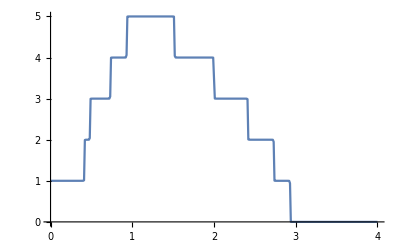
{536.98,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
χ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
χχ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
Clear[kk41,kk42,kk43,kk44,kk45,kk46,kk47,kk48,kk49,kk410,kk411,kk412,kk413,kk414]
```

```mathematica
k414[ω_,ϵ1_]:=k414[ω,ϵ1]=Append[{},Table[χ14[ω,0.001,1,0,ϵ1],{i,50}]];
k413[ω_,ϵ1_]:=k413[ω,ϵ1]=Append[{},Table[χ13[ω,0.001,1,0,ϵ1],{i,50}]];
k412[ω_,ϵ1_]:=k412[ω,ϵ1]=Append[{},Table[χ12[ω,0.001,1,0,ϵ1],{i,50}]];
k411[ω_,ϵ1_]:=k411[ω,ϵ1]=Append[{},Table[χ11[ω,0.001,1,0,ϵ1],{i,50}]];
k410[ω_,ϵ1_]:=k410[ω,ϵ1]=Append[{},Table[χ10[ω,0.001,1,0,ϵ1],{i,50}]];
k49[ω_,ϵ1_]:=k49[ω,ϵ1]=Append[{},Table[χ9[ω,0.001,1,0,ϵ1],{i,50}]];
k48[ω_,ϵ1_]:=k48[ω,ϵ1]=Append[{},Table[χ8[ω,0.001,1,0,ϵ1],{i,50}]];
k47[ω_,ϵ1_]:=k47[ω,ϵ1]=Append[{},Table[χ7[ω,0.001,1,0,ϵ1],{i,50}]];
k46[ω_,ϵ1_]:=k46[ω,ϵ1]=Append[{},Table[χ6[ω,0.001,1,0,ϵ1],{i,50}]];
k45[ω_,ϵ1_]:=k45[ω,ϵ1]=Append[{},Table[χ5[ω,0.001,1,0,ϵ1],{i,50}]];
k44[ω_,ϵ1_]:=k44[ω,ϵ1]=Append[{},Table[χ4[ω,0.001,1,0,ϵ1],{i,50}]];
k43[ω_,ϵ1_]:=k43[ω,ϵ1]=Append[{},Table[χ3[ω,0.001,1,0,ϵ1],{i,50}]];
k42[ω_,ϵ1_]:=k42[ω,ϵ1]=Append[{},Table[χ2[ω,0.001,1,0,ϵ1],{i,50}]];
k41[ω_,ϵ1_]:=k41[ω,ϵ1]=Append[{},Table[χ1[ω,0.001,1,0,ϵ1],{i,50}]];
kk414[ω_,ϵ1_]:=kk414[ω,ϵ1]=Append[{},Table[χχ14[ω,0.001,1,0,ϵ1],{i,50}]];
kk413[ω_,ϵ1_]:=kk413[ω,ϵ1]=Append[{},Table[χχ13[ω,0.001,1,0,ϵ1],{i,50}]];
kk412[ω_,ϵ1_]:=kk412[ω,ϵ1]=Append[{},Table[χχ12[ω,0.001,1,0,ϵ1],{i,50}]];
kk411[ω_,ϵ1_]:=kk411[ω,ϵ1]=Append[{},Table[χχ11[ω,0.001,1,0,ϵ1],{i,50}]];
kk410[ω_,ϵ1_]:=kk410[ω,ϵ1]=Append[{},Table[χχ10[ω,0.001,1,0,ϵ1],{i,50}]];
kk49[ω_,ϵ1_]:=kk49[ω,ϵ1]=Append[{},Table[χχ9[ω,0.001,1,0,ϵ1],{i,50}]];
kk48[ω_,ϵ1_]:=kk48[ω,ϵ1]=Append[{},Table[χχ8[ω,0.001,1,0,ϵ1],{i,50}]];
kk47[ω_,ϵ1_]:=kk47[ω,ϵ1]=Append[{},Table[χχ7[ω,0.001,1,0,ϵ1],{i,50}]];
kk46[ω_,ϵ1_]:=kk46[ω,ϵ1]=Append[{},Table[χχ6[ω,0.001,1,0,ϵ1],{i,50}]];
kk45[ω_,ϵ1_]:=kk45[ω,ϵ1]=Append[{},Table[χχ5[ω,0.001,1,0,ϵ1],{i,50}]];
kk44[ω_,ϵ1_]:=kk44[ω,ϵ1]=Append[{},Table[χχ4[ω,0.001,1,0,ϵ1],{i,50}]];
kk43[ω_,ϵ1_]:=kk43[ω,ϵ1]=Append[{},Table[χχ3[ω,0.001,1,0,ϵ1],{i,50}]];
kk42[ω_,ϵ1_]:=kk42[ω,ϵ1]=Append[{},Table[χχ2[ω,0.001,1,0,ϵ1],{i,50}]];
kk41[ω_,ϵ1_]:=kk41[ω,ϵ1]=Append[{},Table[χχ1[ω,0.001,1,0,ϵ1],{i,50}]]
```

```mathematica
ρ4[ω_,ϵ1_]:=Join[Mean[k41[ω,ϵ1]],Mean[k42[ω,ϵ1]],Mean[k43[ω,ϵ1]],Mean[k44[ω,ϵ1]],Mean[k45[ω,ϵ1]],Mean[k46[ω,ϵ1]],Mean[k47[ω,ϵ1]],Mean[k48[ω,ϵ1]],Mean[k49[ω,ϵ1]],Mean[k410[ω,ϵ1]],Mean[k411[ω,ϵ1]],Mean[k413[ω,ϵ1]],Mean[k414[ω,ϵ1]],Mean[kk41[ω,ϵ1]],Mean[kk42[ω,ϵ1]],Mean[kk43[ω,ϵ1]],Mean[kk44[ω,ϵ1]],Mean[kk45[ω,ϵ1]],Mean[kk46[ω,ϵ1]],Mean[kk47[ω,ϵ1]],Mean[kk48[ω,ϵ1]],Mean[kk49[ω,ϵ1]],Mean[kk410[ω,ϵ1]],Mean[kk411[ω,ϵ1]],Mean[kk413[ω,ϵ1]],Mean[kk414[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ4[1.5,0.5]]]
```

{34.1312,3.36421}

```mathematica
Export["4imp3.csv",Table[{ω,Mean[ρ4[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

4imp3.csv

```mathematica
Export["4imp4.csv",Table[{ω,Mean[ρ4[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

4imp4.csv

```mathematica
Export["4imp5.csv",Table[{ω,Mean[ρ4[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

4imp5.csv

```mathematica
Export["4imp6.csv",Table[{ω,Mean[ρ4[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

4imp6.csv

```mathematica
Export["4imp7.csv",Table[{ω,Mean[ρ4[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

4imp7.csv

```mathematica
Export["4imp8.csv",Table[{ω,Mean[ρ4[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

4imp8.csv

```mathematica
Export["4imp9.csv",Table[{ω,Mean[ρ4[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

4imp9.csv

```mathematica
Export["4imp1.csv",Table[{ω,Mean[ρ4[ω,1]]},{ω,Range[0,4,0.01]}]]
```

4imp1.csv

```mathematica
Import["4imp1.csv"]
```

Import::nffil: File 4imp1.csv not found during Import.

$Failed

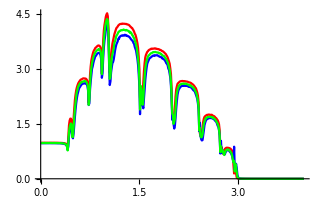

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/11AGNR/4imp/4imp6.csv"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/11AGNR/6imp/6imp6.csv"],PlotStyle->Blue],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/11AGNR/5imp/5imp6.csv"],PlotStyle->Green]]
```

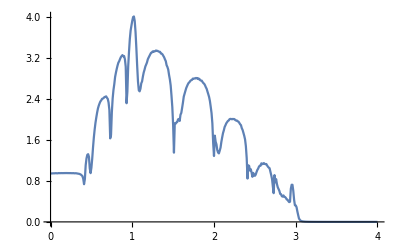

```mathematica
ListPlot[%115,Joined->True]
```